```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yuichirotada/Documents/Univ/DECIGO/math

```mathematica
ρinteg[x_,T_]=(*(x^(1/2)(x+2/T)^(1/2)(x+1/T)^2)/(Exp[x+1/T]+1)*)(x^2 Sqrt[x^2+1/T^2])/(Exp[Sqrt[x^2+1/T^2]]+1);
pinteg[x_,T_]=(*(x^(3/2)(x+2/T)^(3/2))/(Exp[x+1/T]+1)*)(x^4(x^2+1/T^2)^(-1/2))/(Exp[Sqrt[x^2+1/T^2]]+1);
```

```mathematica
AbsoluteTiming[ρList=Table[{10^lnT,NIntegrate[ρinteg[x,10^lnT],{x,0,1000},WorkingPrecision->30]},{lnT,-2,5,10^-2}];
pList=Table[{10^lnT,NIntegrate[pinteg[x,10^lnT],{x,0,1000},WorkingPrecision->30]},{lnT,-2,5,10^-2}];]
```

{14.9418,Null}

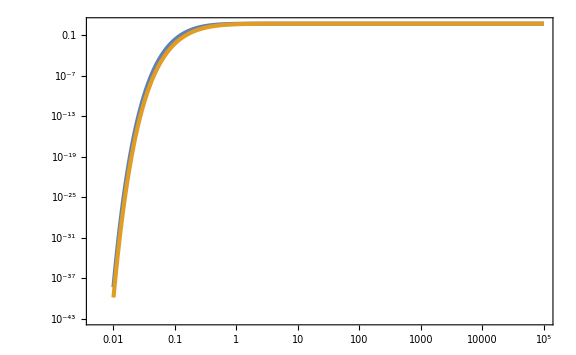

```mathematica
ListLogLogPlot[{ρList,pList}]
```

```mathematica
ρintegint[T_]=Interpolation[ρList][T];
pintegint[T_]=Interpolation[pList][T];
```

## Fiducial

```mathematica
gSM=10675/100;
gDM=2 2 10;
```

```mathematica
ρ[T_]:=π^2/30 gSM T^4+T^4/(2 π^2)ρintegint[T]gDM/;T>=10^-2
ρ[T_]:=π^2/30 gSM T^4/;T<10^-2
ρp[T_]:=π^2/30 gSM 4 T^3+ 4 T^3/(2 π^2)ρintegint[T]gDM+T^4/(2 π^2)ρintegint'[T]gDM/;T>=10^-2
ρp[T_]:=π^2/30 gSM 4 T^3/;T<10^-2
p[T_]:=1/3 π^2/30 gSM T^4+T^4/(6 π^2)pintegint[T]gDM/;T>=10^-2
p[T_]:=1/3 π^2/30 gSM T^4/;T<10^-2
pp[T_]:=1/3 π^2/30 gSM 4 T^3+4 T^3/(6 π^2)pintegint[T]gDM+T^4/(6 π^2)pintegint'[T]gDM/;T>=10^-2
pp[T_]:=1/3 π^2/30 gSM 4 T^3/;T<10^-2
s[T_]:=(ρ[T]+p[T])/T
w[T_]:=p[T]/ρ[T]
cs2[T_]:=pp[T]/ρp[T]
gr[T_]:=ρ[T]/(π^2/30 T^4)
gs[T_]:=s[T]/((2 π^2)/45 T^3)
```

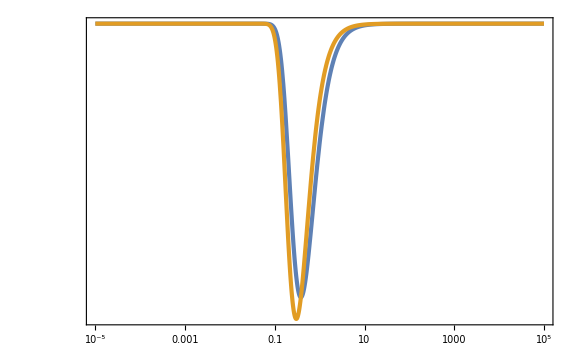

```mathematica
LogLogPlot[{w[T],cs2[T]},{T,10^-5,10^5},PlotRange->Full]
```

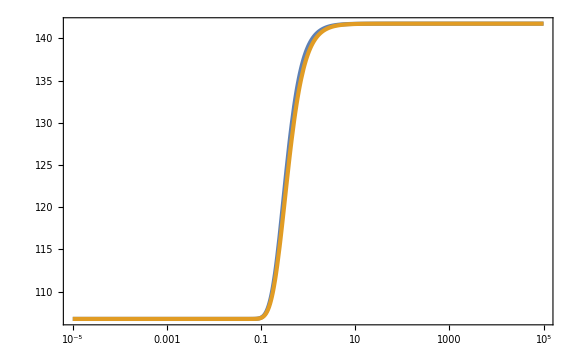

```mathematica
LogLinearPlot[{gr[T],gs[T]},{T,10^-5,10^5}]
```

```mathematica
Mf=10^7;
fout=2.7 10^-5(Tout Mf)/10^3(gSM/128)^(1/6)
```

0.261953 Tout

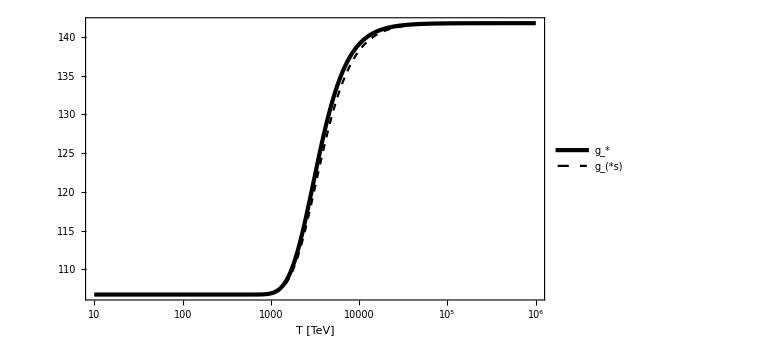

```mathematica
LogLinearPlot[{gr[10^3 T/Mf],gs[10^3 T/Mf]},{T,10^1,10^6},GridLines->{{10^-3 Mf},None},PlotStyle->{{Black,AbsoluteThickness[3]},{Black,Dashed}},FrameLabel->{"T [TeV]",None},PlotLegends->Placed[{"g_*","g_(*s)"},{0.8,0.2}]]
```

```mathematica
Tin=10^5;
Tout=10^-5;
ain=1;
sin=s[Tin]
a[T_]:=ain sin^(1/3)/s[T]^(1/3)
```

6.21785077266962926319918931474×10^16

```mathematica
AbsoluteTiming[NρList=Table[{Log[a[10^lnT]],ρ[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NwList=Table[{Log[a[10^lnT]],w[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NgrList=Table[{Log[a[10^lnT]],gr[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NgsList=Table[{Log[a[10^lnT]],gs[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;]
```

{8.57214,Null}

```mathematica
ρint[NN_]=Interpolation[NρList][NN];
wint[NN_]=Interpolation[NwList][NN];
grint[NN_]=Interpolation[NgrList][NN];
gsint[NN_]=Interpolation[NgsList][NN];
```

```mathematica
Nout=Log[a[Tout]]//Quiet
```

23.120376026772605860925213207311

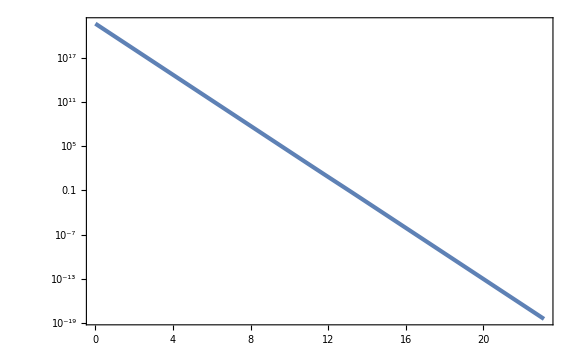

```mathematica
LogPlot[ρint[NN],{NN,0,Nout}]
```

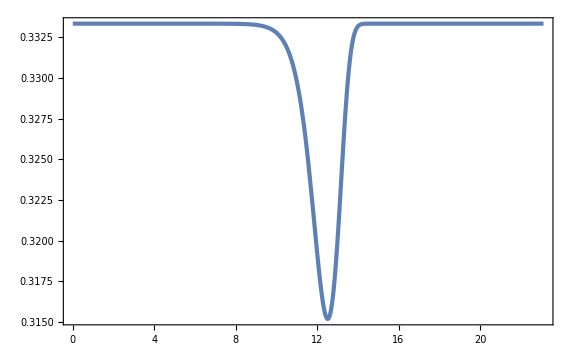

```mathematica
Plot[wint[NN],{NN,0,Nout},PlotRange->Full]
```

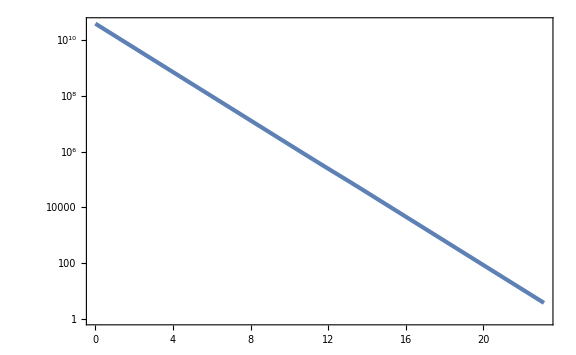

```mathematica
LogPlot[Exp[NN]Sqrt[ρint[NN]/3],{NN,0,Nout}]
```

```mathematica
TkList=ParallelTable[Tp0=0;
ks=Exp[Nk]Sqrt[ρint[Nk]/3];
Ni=Nk-5;(*Nf=Nk+5;*)
sol=NDSolve[{T''[NN]+3/2(1-wint[NN])T'[NN]+k^2/(Exp[2NN]ρint[NN]/3)T[NN]==0/.{k->ks},T[0]==1,T'[0]==0,WhenEvent[T''[NN]==0,Tp0++;If[Tp0>=10,Nfs=NN;"StopIntegration"]]},T'[NN],{NN,0,Nout},WorkingPrecision->30,MaxSteps->100000][[1]]//Quiet;
Tpsol[NN_]=T'[NN]/.sol;
{ks/(a[Tout]Sqrt[ρ[Tout]/3]),Tpsol[Nfs]^2(grint[Nfs] gsint[Nfs]^(-4/3))/106.75^(-1/3)}
,{Nk,7,18,10^-1}];//AbsoluteTiming
```

{24.9889,Null}

```mathematica
OGWg=Table[{(Exp[Nk]Sqrt[ρint[Nk]/3])/(a[Tout]Sqrt[ρ[Tout]/3]),(grint[Nk] gsint[Nk]^(-4/3))/106.75^(-1/3)},{Nk,7,18,0.01}];
```

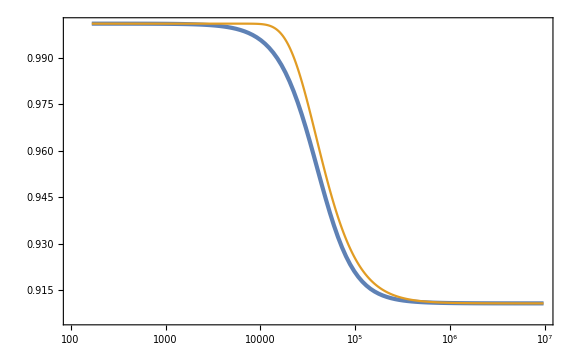

```mathematica
Show[ListLogLinearPlot[TkList],ListLogLinearPlot[OGWg.{{1,0},{0,Last[TkList][[2]]}},PlotStyle->Color[2]]]
```

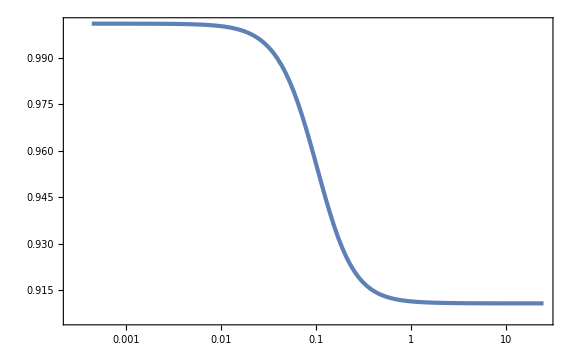

```mathematica
ListLogLinearPlot[TkList.{{fout,0},{0,1}}]
```

```mathematica
Export["Tkfiducial.csv",TkList];
```

## TkList

```mathematica
Fnum=20;
```

### TkList

```mathematica
gSM=10675/100;
gDM=2 2 Fnum;
```

```mathematica
ρ[T_]:=π^2/30 gSM T^4+T^4/(2 π^2)ρintegint[T]gDM/;T>=10^-2
ρ[T_]:=π^2/30 gSM T^4/;T<10^-2
ρp[T_]:=π^2/30 gSM 4 T^3+ 4 T^3/(2 π^2)ρintegint[T]gDM+T^4/(2 π^2)ρintegint'[T]gDM/;T>=10^-2
ρp[T_]:=π^2/30 gSM 4 T^3/;T<10^-2
p[T_]:=1/3 π^2/30 gSM T^4+T^4/(6 π^2)pintegint[T]gDM/;T>=10^-2
p[T_]:=1/3 π^2/30 gSM T^4/;T<10^-2
pp[T_]:=1/3 π^2/30 gSM 4 T^3+4 T^3/(6 π^2)pintegint[T]gDM+T^4/(6 π^2)pintegint'[T]gDM/;T>=10^-2
pp[T_]:=1/3 π^2/30 gSM 4 T^3/;T<10^-2
s[T_]:=(ρ[T]+p[T])/T
w[T_]:=p[T]/ρ[T]
cs2[T_]:=pp[T]/ρp[T]
gr[T_]:=ρ[T]/(π^2/30 T^4)
gs[T_]:=s[T]/((2 π^2)/45 T^3)
```

```mathematica
Tin=10^5;
Tout=10^-5;
ain=1;
sin=s[Tin]
a[T_]:=ain sin^(1/3)/s[T]^(1/3)
```

7.75312256837797393724023678842×10^16

```mathematica
AbsoluteTiming[NρList=Table[{Log[a[10^lnT]],ρ[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NwList=Table[{Log[a[10^lnT]],w[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NgrList=Table[{Log[a[10^lnT]],gr[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;
NgsList=Table[{Log[a[10^lnT]],gs[10^lnT]},{lnT,Log[Tout],Log[Tin],10^-2}]//Quiet;]
```

{8.91391,Null}

```mathematica
ρint[NN_]=Interpolation[NρList][NN];
wint[NN_]=Interpolation[NwList][NN];
grint[NN_]=Interpolation[NgrList][NN];
gsint[NN_]=Interpolation[NgsList][NN];
```

```mathematica
Nout=Log[a[Tout]]//Quiet
```

23.193933147495006459886959577341

```mathematica
TkList=ParallelTable[Tp0=0;
ks=Exp[Nk]Sqrt[ρint[Nk]/3];
Ni=Nk-5;(*Nf=Nk+5;*)
sol=NDSolve[{T''[NN]+3/2(1-wint[NN])T'[NN]+k^2/(Exp[2NN]ρint[NN]/3)T[NN]==0/.{k->ks},T[0]==1,T'[0]==0,WhenEvent[T''[NN]==0,Tp0++;If[Tp0>=10,Nfs=NN;"StopIntegration"]]},T'[NN],{NN,0,Nout},WorkingPrecision->30,MaxSteps->100000][[1]]//Quiet;
Tpsol[NN_]=T'[NN]/.sol;
{ks/(a[Tout]Sqrt[ρ[Tout]/3]),Tpsol[Nfs]^2(grint[Nfs] gsint[Nfs]^(-4/3))/106.75^(-1/3)}
,{Nk,7,18,10^-1}];//AbsoluteTiming
```

{24.1603,Null}

```mathematica
Export["Tk_"<>ToString[Fnum]<>".csv",TkList];
```

## Forecast

```mathematica
TkData=Table[Sort[Import["Tk_"<>ToString[NF]<>".csv"]],{NF,1,20}];
```

```mathematica
TkList[k_]=Table[Interpolation[TkData[[NF]]][k](1-UnitStep[First[TkData[[NF]]][[1]]-k])(1-UnitStep[k-Last[TkData[[NF]]][[1]]])+UnitStep[First[TkData[[NF]]][[1]]-k]First[TkData[[NF]]][[2]]+UnitStep[k-Last[TkData[[NF]]][[1]]]Last[TkData[[NF]]][[2]],{NF,1,20}];
```

```mathematica
Fnum=10;
TkF[k_]=TkList[k][[Fnum]];
```

InterpolatingFunction::dmval: Input value {1.00047} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

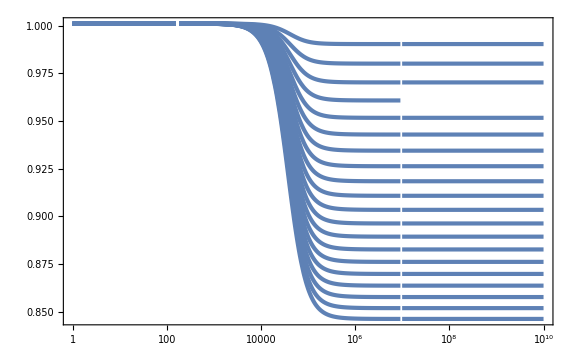

```mathematica
LogLinearPlot[TkList[k],{k,1,10^10}]
```

```mathematica
fout[Mf_]=2.7 10^-5(Tout Mf)/10^3(gSM/128)^(1/6)/.{gSM->106.75,Tout->10^-5};
Mfid=10^7;
```

```mathematica
10^5 fout[Mfid]
```

0.261953

```mathematica
dOGW[f_,Nf_,Mf_,OGWlow_]:=(TkList[f/fout[Mf]][[Nf]]-TkF[f/fout[Mfid]])OGWlow;
```

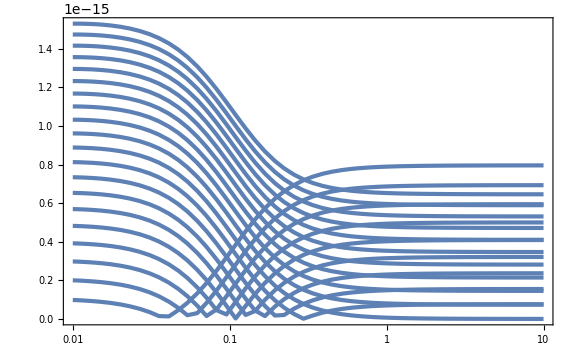

```mathematica
LogLinearPlot[Table[Abs[dOGW[f,Nf,10^5,10^-14]],{Nf,1,20}],{f,0.01,10}]
```

```mathematica
freq=10^Range[-2,1,0.01];
```

```mathematica
fp=7.5;
```

```mathematica
SnBDECIGO[f_]:=1.4*10^-45(1 + (f/fp)^2) + 1.7*10^-47 f^-4(1 + (f/fp)^2)^-1 + 1.0*10^-44*(f/0.1)^-16
SnDECIGO[f_]:=1.8*10^-47(1 + (f/fp)^2) + 1.2*10^-50 f^-4(1 + (f/fp)^2)^-1 +  1.0*10^-46*(f/0.1)^-16
```

```mathematica
Tobs=3.0*3.154*10^7 (* year in seconds *);
hubble=0.68;
H0=hubble*3.2408629736704004*10^-18;(* Hubble [/s] *)
```

```mathematica
SNRBDECIGO[Nf_,Mf_,OGWlow_]:=(3 H0^2)/(4 π^2)Sqrt[2Tobs]Sqrt[NIntegrate[(dOGW[E^lnf,Nf,Mf,OGWlow]^2)/(E^(5lnf)SnBDECIGO[E^lnf]^2),{lnf,Log[0.01],Log[10]}]]
SNRDECIGO[Nf_,Mf_,OGWlow_]:=(3 H0^2)/(4 π^2)Sqrt[2Tobs]Sqrt[NIntegrate[(dOGW[E^lnf,Nf,Mf,OGWlow]^2)/(E^(5lnf)SnDECIGO[E^lnf]^2),{lnf,Log[0.01],Log[10]}]]
```

```mathematica
OmegaGWBDECIGO[f_]:=(4 π^2)/(3 H0^2 √Tobs)√(f^5 SnBDECIGO[f]^2)
OmegaGWDECIGO[f_]:=(4 π^2)/(3 H0^2 √Tobs)√(f^5 SnDECIGO[f]^2)
```

```mathematica
OGWDList=Table[{E^lnf,OmegaGWDECIGO[E^lnf]},{lnf,Log[0.01],Log[10],10^-2}];
```

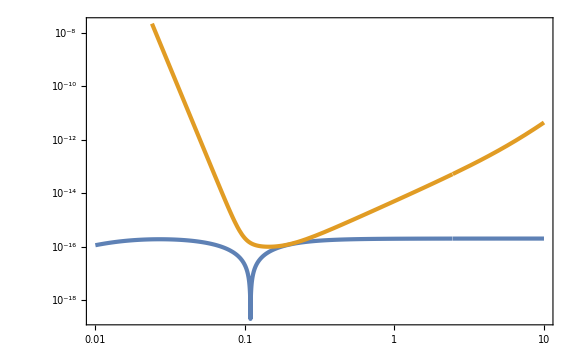

```mathematica
LogLogPlot[{Abs[dOGW[f,5,10^6,5 10^-15]],OmegaGWDECIGO[f]},{f,10^-2,10}]
```

```mathematica
SNRList=Flatten[ParallelTable[{lnMf-3,Nf,SNRDECIGO[Nf,10^lnMf,5 10^-15]//Quiet},{Nf,1,20},{lnMf,5,8,10^-2}],1];//AbsoluteTiming
```

{143.2,Null}

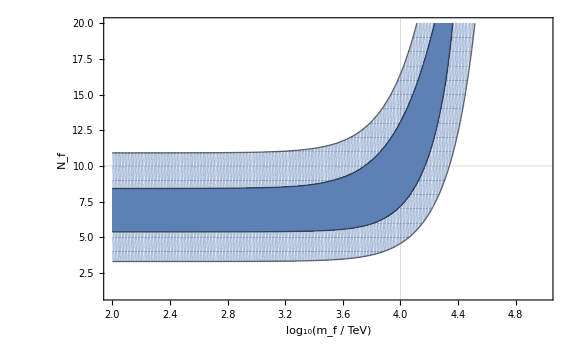

```mathematica
ListContourPlot[SNRList,Contours->{1,2},GridLines->{{Log10[Mfid]-3},{Fnum}},ContourShading->{Color[1],Directive[Color[1],Opacity[0.2]],None},PlotRangePadding->None,FrameLabel->{Row[{"log_10(",Subscript[m, "f"]," / TeV)"}],Subscript[N, "f"]}]
```